# Comparison of Potential between Full Model and Simple Model

Isaac R. Wang

This code compared the potential of the full ALP model and the simple model, which corresponds to the f_a->0 limit of the ALP model. The computation is simplified. For full analysis of the full model, see Zero_T_full_model.nb.
We use a benchmark point: f=f_c, m_s=5 GeV, sinθ=0.1, β=π/10  as an example. At this point, the full ALP model will give SFOPT however the simple model will not.

```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={{μH,λ,μS,A,x1,x2,x3,h,v,w,mS,mh,θ,f,f-S,μHsq,μSsq}∈PositiveReals,0<δ<π/2};
MakeBoxes[μSsq,TraditionalForm]:="μ_S^2";
MakeBoxes[μHsq,TraditionalForm]:="μ_H^2";
MakeBoxes[x1,TraditionalForm]:="x_1";
MakeBoxes[x2,TraditionalForm]:="x_2";
MakeBoxes[x3,TraditionalForm]:="x_3";
MakeBoxes[mh,TraditionalForm]:="m_h";
MakeBoxes[mS,TraditionalForm]:="m_S";
```

## Tree-level potential

```mathematica
V‵ALP‵0=-1/2(μHsq-A f Cos[δ])h^2+1/4 λ h^4+μSsq f^2(1-Cos[S/f])-1/2 A f( h^2-2 v^2)Cos[S/f-δ];
V‵Sim‵0=-1/2 μHsq h^2+1/4 λ h^4-1/2 A S (h^2-2 v^2)+1/2 μSsq S^2;
sol‵tree={A->(Csc[δ]Sin[θ]Cos[θ](mh^2-mS^2))/(√2 v),μSsq->1/2(Cos[2θ](mS^2-mh^2)+mh^2+mS^2),λ->(Cos[2θ](mh^2-mS^2)+mh^2+mS^2)/(8 v^2),μHsq->1/4(Cos[2θ](mh^2-mS^2)+mh^2+mS^2)};
```

## 1-loop CW

### SM parameters

```mathematica
(*Parameter input and integral definition*)
mW=80.379;
mZ=91.1876;
mt=172.69;
αsmZ=0.1184;
g3mZ=√(4π αsmZ);
GF=1.1663787×10^-5;
vnum=(√2 GF)^(-1/2);
mhpole=125.13;
(*Define integrals. The scale is fixed to be mZ*)
A0[M_]:=M^2(1-Log[M^2/mZ^2]);
B0[p_,M1_,M2_]:=-NIntegrate[Log[(x M1^2+(1-x)M2^2-x(1-x)p^2)/mZ^2],{x,0,1}]
ytmZ=2(GF/(√2)mt^2)^(1/2)+mt/(√2 vnum^3(4π)^2)(-(mhpole^2-4 mt^2)B0[mt,mhpole,mt]+(mt^2(80 mW^2 mZ^2-64 mW^4-7 mZ^4)+40 mW^2 mZ^4-32 mW^4 mZ^2-17 mZ^6)/(9 mt^2 mZ^2)B0[mt,mt,mZ]+(mt^2 mW^2+mt^4-2 mW^4)/mt^2 B0[mt,0,mW]+((3 mhpole^2)/(mhpole^2-mW^2)+2 mW^2/mt^2+3 mW^2/(mW^2-mZ^2)-10)A0[mW]+(3 mW^2/(mW^2-mhpole^2)+1)A0[mhpole]+(36 mt^2 mZ^2-56 mW^2 mZ^2+64 mW^4-17 mZ^4)/(9 mt^2 mZ^2)A0[mt]+((3 mW^2)/(mZ^2-mW^2)+(32 mW^4-40 mW^2 mZ^2+17 mZ^4)/(9 mt^2 mZ^2)-3)A0[mZ]+mhpole^2/2-3 mt^2-9 mW^2+7 mZ^2/18+64 mW^4/(9 mZ^2))+mt/(√2 vnum (4π))αsmZ(-8 A0[mt]/mt^2-8/3)//Re;
g2mZ=2(√2 GF)^(1/2)mW+2 mW/((4π)^2 vnum^3)((mhpole^4/(6 mW^2)-2 mhpole^2/3+2 mW^2)B0[mW,mhpole,mW]+(-mt^4/mW^2-mt^2+2 mW^2)B0[mW,0,mt]+1/6(-48 mW^4/mZ^2+mZ^4/mW^2-68 mW^2+16 mZ^2)B0[mW,mW,mZ]+1/6(mhpole^2(9/(mhpole^2-mW^2)+1/mW^2)+mZ^2/mW^2+mW^2(9/(mW^2-mZ^2)+48/mZ^2)-27)A0[mW]+(2-(mhpole^2(mhpole^2+8 mW^2))/(6 mW^2(mhpole^2-mW^2)))A0[mhpole]+(mt^2/mW^2+1)A0[mt]+1/6(24 mW^2/mZ^2-mZ^2/mW^2+9 mW^2/(mZ^2-mW^2)-17)A0[mW]+1/36(-3 mhpole^2+18 mt^2+288 mW^4/mZ^2-374 mW^2-3 mZ^2))//Re;
g1mZ=2(√2 GF)^(1/2)√(mZ^2-mW^2)+(2 √(mZ^2-mW^2))/((4π)^2 vnum^3)((88/9-(124 mW^2)/(9 mZ^2)+(mhpole^2+34 mW^2)/(6(mZ^2-mW^2)))A0[mZ]+(mhpole^2-4 mW^2)/(2(mhpole^2-mW^2))A0[mhpole]+(-7/9-mt^2/(mZ^2-mW^2)+64 mW^2/(9 mZ^2))A0[mt]+(mhpole^4+2 mW^2(mW^2-15 mZ^2)+3 mhpole^2(2 mW^2+7 mZ^2))/(6(mhpole^2-mW^2)(mW^2-mZ^2))A0[mW]-(mt^4+mW^2 mt^2-2 mW^4)/(mW^2-mZ^2)B0[mW,0,mt]-(mhpole^4-4 mZ^2 mhpole^2+12 mZ^4)/(6(mW^2-mZ^2))B0[mZ,mhpole,mZ]+(mhpole^4-4 mW^2 mhpole^2+12 mW^4)/(6(mW^2-mZ^2))B0[mW,mhpole,mW]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mW^2-mZ^2))B0[mW,mW,mZ]+1/9(-23 mW^2+7 mt^2+17 mZ^2-(64 mt^2 mW^2)/mZ^2-(9 mW^2(mt^2-mW^2))/(mZ^2-mW^2))B0[mZ,mt,mt]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mZ^2-mW^2))B0[mZ,mW,mW]+1/36(576 mW^4/mZ^2-242 mW^2-3 mhpole^2+257 mZ^2+36 mW^2/(mZ^2-mW^2)+mt^2(82-256 mW^2/mZ^2)))//Re;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24537+2.46099 ⅈ and 0.000286423 for the integral and error estimates.

### CW correction and renormalization

```mathematica
mWsq[h_]:=1/4 g2mZ^2 h^2;
mZsq[h_]:=1/4(g2mZ^2+g1mZ^2)h^2;
mtsq[h_]:=1/2 ytmZ^2 h^2;
VCW[h_]:=1/(64 π^2)(6 mWsq[h]^2(Log[mWsq[h]/mZ^2]-5/6)+3 mZsq[h]^2(Log[mZsq[h]/mZ^2]-5/6)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2));
Vloop‵ALP[h_,S_]=(V‵ALP‵0/.{v->v/(√2)}/.{v->vnum})+VCW[h]//Simplify;
Vloop‵Sim[h_,S_]=(V‵Sim‵0/.{v->v/(√2)}/.{v->vnum})+VCW[h]//Simplify;
```

```mathematica
P={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
Diag‵mass={{mh^2,0},{0,mS^2}};
rotated=P.Diag‵mass.Inverse[P]//Simplify;
```

```mathematica
mass‵ALP=D[Vloop‵ALP[h,S]//Simplify,{{h,S},2}]/.{h->vnum,S->0}
mass‵Sim=D[Vloop‵Sim[h,S]//Simplify,{{h,S},2}]/.{h->vnum,S->0}
der‵ALP=D[Vloop‵ALP[h,S],{{h,S}}]/.{h->vnum,S->0}//Simplify
der‵Sim=D[Vloop‵Sim[h,S],{{h,S}}]/.{h->vnum,S->0}//Simplify
```

(181872. λ-1. μ_H^2-2862.09 | -246.22 A sin(δ)
-246.22 A sin(δ) | 1. μ_S^2+0.)

(2 (0.-0.5 μ_H^2)+727489. (0.25 λ+0.0465372)-36717.4 | -246.22 A
-246.22 A | 1. μ_S^2)

{1.49268×10^7 λ-246.22 μ_H^2-69945.5,0.}

{1.49268×10^7 λ-246.22 μ_H^2-69945.5,0.}

```mathematica
D[Vloop‵ALP[h,S],{{h,S}}]//Simplify
```

{h (1. A f cos(δ)-1. A f cos(S/f-δ)+1. h^2 λ+0.177861 h^2-0.0331527 h^2 log(h)-1. μ_H^2),A (0.5 h^2-30312.1) sin(S/f-δ)+1. f μ_S^2 sin(S/f)}

## Benchmark: m_S=5GeV, δ=2π/5, f=3 f_c, sinθ=0.1

```mathematica
{Atree,λtree,μSsqtree,μHsqtree}={A,λ,μSsq,μHsq}/.sol‵tree/.{mh->mhpole,v->v/(√2)}/.{v->vnum}/.{mS->5,δ->(2π)/5,θ->ArcSin[0.1]};
{ASimtree}={A}/.sol‵tree/.{mh->mhpole,v->v/(√2)}/.{v->vnum}/.{mS->5,θ->ArcSin[0.1],δ->π/2}(*δ->π/2 is the limit where we can go back to the simple model*);
fc=Atree/μSsqtree(vnum/(√2))^2 Sin[(2π)/5];
benchmark={mS->5,δ->(2π)/5,f->3fc,θ->ArcSin[0.1]};
```

```mathematica
mass‵ALP‵num=mass‵ALP/.benchmark
mass‵Sim‵num=mass‵Sim/.benchmark//Simplify
der‵ALP‵num=der‵ALP/.benchmark;
der‵Sim‵num=der‵Sim/.benchmark;
rotated‵num=rotated/.benchmark/.{mh->mhpole};
```

(181872. λ-1. μ_H^2-2862.09 | -234.169 A
-234.169 A | 1. μ_S^2+0.)

(181872. λ-1. μ_H^2-2862.09 | -246.22 A
-246.22 A | 1. μ_S^2)

```mathematica
sol‵ALP=NSolve[{rotated‵num[[1,1]]==mass‵ALP‵num[[1,1]],rotated‵num[[1,2]]==mass‵ALP‵num[[1,2]],rotated‵num[[2,2]]==mass‵ALP‵num[[2,2]],der‵ALP‵num[[1]]==0},{λ,A,μHsq,μSsq}][[1]]
sol‵Sim=NSolve[{rotated‵num[[1,1]]==mass‵Sim‵num[[1,1]],rotated‵num[[1,2]]==mass‵Sim‵num[[1,2]],rotated‵num[[2,2]]==mass‵Sim‵num[[2,2]],der‵Sim‵num[[1]]==0},{λ,A,μHsq,μSsq}][[1]]
```

{λ→0.149109,A→6.64228,μ_H^2→8755.52,μ_S^2→181.325}

{λ→0.149109,A→6.31719,μ_H^2→8755.52,μ_S^2→181.325}

```mathematica
3*fc
```

3168.13

```mathematica
der‵Sim‵num
```

{1.49268×10^7 λ-246.22 μ_H^2-69945.5,0.}

```mathematica
der‵ALP‵num
```

{1.49268×10^7 λ-246.22 μ_H^2-69945.5,0.}

```mathematica
V0T‵Sim[h_,S_]=V‵Sim‵0+Vloop‵Sim[h,S]/.sol‵Sim/.benchmark/.v->v/(√2)/.v->vnum;
V0T‵ALP[h_,S_]=V‵ALP‵0+Vloop‵ALP[h,S]/.sol‵ALP/.benchmark/.v->v/(√2)/.v->vnum;
```

## Finite temperature correction

```mathematica
Jbdata=Import[NotebookDirectory[]<>"finiteT_b.dat.txt","Table"];
Jfdata=Import[NotebookDirectory[]<>"finiteT_f.dat.txt","Table"];
JBfit[x_]=Interpolation[Jbdata][x];
JFfit[x_]=Interpolation[Jfdata][x];
```

```mathematica
mWL[h_,T_]=1/4 g2mZ^2 h^2+11/6 g2mZ^2 T^2;
mgauge=({{g2mZ^2 x1^2/4+11/6 g2mZ^2 x2^2, -g2mZ g1mZ x1^2/4}, {-g2mZ g1mZ x1^2/4, g1mZ^2 x1^2/4+11/6 g1mZ^2 x2^2}});
gaugeL=Eigenvalues[mgauge]//FullSimplify;
mBL[h_,T_]=gaugeL[[1]]/.{x1->h,x2->T};
mZL[h_,T_]=gaugeL[[2]]/.{x1->h,x2->T};
VCW‵resum[h_,S_,T_]:=1/(64 π^2)(4 mWsq[h]^2(Log[mWsq[h]/mZ^2]-1/2)+2 mWL[h,T]^2(Log[mWL[h,T]/mZ^2]-3/2)+2 mZsq[h]^2(Log[mZsq[h]/mZ^2]-1/2)+mZL[h,T]^2(Log[mZL[h,T]/mZ^2]-3/2)+mBL[h,T]^2(Log[mBL[h,T]/mZ^2]-3/2)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2));
VFT[h_,S_,T_]:=T^4/(2 π^2)(4JBfit[mWsq[h]/T^2]+2JBfit[mWL[h,T]/T^2]+2JBfit[mZsq[h]/T^2]+JBfit[mZL[h,T]/T^2]+JBfit[mBL[h,T]/T^2]+12JFfit[mtsq[h]/T^2]);
Vtot‵ALP[h_,S_,T_]=VFT[h,S,T]+(V‵ALP‵0/.{v->v/(√2)}/.{v->vnum}/.benchmark/.sol‵ALP)+VCW‵resum[h,S,T];
Vtot‵Sim[h_,S_,T_]=VFT[h,S,T]+(V‵Sim‵0/.{v->v/(√2)}/.{v->vnum}/.sol‵Sim)+VCW‵resum[h,S,T];
```

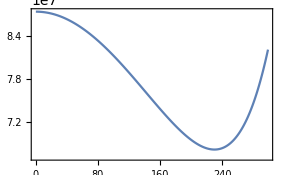

```mathematica
ListLinePlot[Table[{hscan,Minimize[{V‵ALP‵0/.{v->v/(√2)}/.{v->vnum}/.sol‵ALP/.benchmark/.{h->hscan},-3*fc<S<3*fc},S][[1]]},{hscan,10^-5,300,1}]]
```

```mathematica
mindata‵ALP=Flatten[Table[sol=Minimize[{Vtot‵ALP[hscan,S,Tscan],-fc*3<S<fc*3},S];
Smin=S/.sol[[2]];
{hscan,Tscan,Vmin,Smin},
{hscan,10^-5,100,20},{Tscan,40,100,2}],1];
```

```mathematica
Spath‵ALP[h_,T_]=Interpolation[{#1,#2,#4}&@@@mindata‵ALP][h,T];
Vpath‵ALP[h_,T_]=Vtot‵ALP[h,Spath‵ALP[h,T],T]-Vtot‵ALP[10^-5,Spath‵ALP[10^-5,T],T];
```

```mathematica
mindata‵Sim=Flatten[Table[sol=Minimize[{Vtot‵Sim[hscan,S,Tscan],-fc*3<S<fc 3},S];
Smin=S/.sol[[2]];
{hscan,Tscan,Vmin,Smin},
{hscan,10^-5,100,20},{Tscan,40,100,2}],1];
Spath‵Sim[h_,T_]=Interpolation[{#1,#2,#4}&@@@mindata‵Sim][h,T];
Vpath‵Sim[h_,T_]=Vtot‵Sim[h,Spath‵Sim[h,T],T]-Vtot‵Sim[10^-5,Spath‵Sim[10^-5,T],T];
```

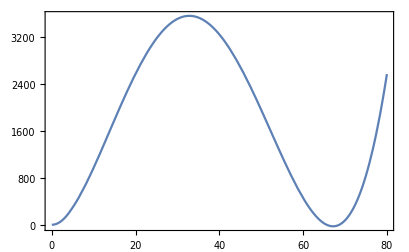

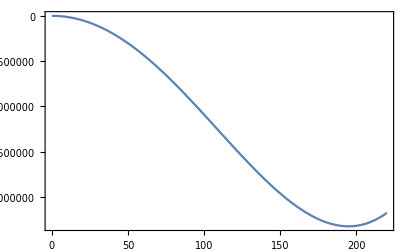

```mathematica
Ttest=66.498;
Plot[Vpath‵ALP[h,Ttest],{h,0,80}]
Plot[Vpath‵Sim[h,Ttest],{h,0,220}]
```

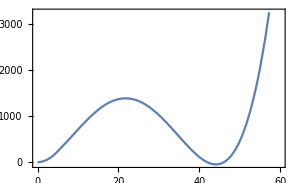

```mathematica
Ttest=82.59;
Plot[Vpath‵Sim[h,Ttest],{h,0,60}]
```

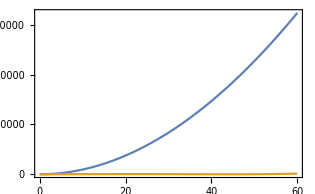

```mathematica
Plot[{Vpath‵ALP[h,Ttest],Vpath‵Sim[h,Ttest]},{h,0,60}]
```

OK we can see that the new model is raised up at large Higgs field value. Thus the PT is delayed until the large field value drops, and the degenerate minima is located at a relatively high higgs field value.

```mathematica
Vtree‵ALP‵1d[h_,T_]=(V‵ALP‵0/. {v->v/Sqrt[2]}/. {v->vnum}/. benchmark/. sol‵ALP/.{S->Spath‵ALP[h,T]})-(V‵ALP‵0/. {v->v/Sqrt[2]}/. {v->vnum}/. benchmark/. sol‵ALP/.{S->Spath‵ALP[10^-5,T]}/.{h->10^-5});
Vtree‵Sim‵1d[h_,T_]=(V‵Sim‵0/.{v->v/(√2)}/.{v->vnum}/.sol‵Sim/.{S->Spath‵Sim[h,T]})-(V‵Sim‵0/.{v->v/(√2)}/.{v->vnum}/.sol‵Sim/.{S->Spath‵Sim[10^-5,T]}/.{h->10^-5});
```

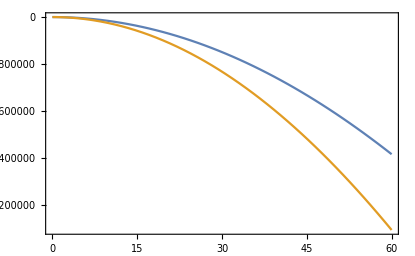

```mathematica
Plot[{Vtree‵ALP‵1d[h,Ttest],Vtree‵Sim‵1d[h,Ttest]},{h,0,60}]
```

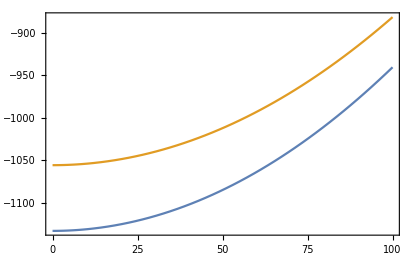

```mathematica
Plot[{Spath‵ALP[h,Ttest],Spath‵Sim[h,Ttest]},{h,0,100}]
```

## Tree-level analysis

```mathematica
VFT‵highT=1/32 T^2 h^2(3 g^2+g1^2+4 yt^2)+h^3 T(-2 g^3-g^2 √(g^2+g1^2)-g1^2 √(g^2+g1^2))/(32π)/.{g->g2mZ,g1->g1mZ,yt->ytmZ}
```

0.16323 h^2 T^2-0.00956371 h^3 T

```mathematica
V0‵ALP‵series=Series[V‵ALP‵0,{S,0,2}]//Normal
```

S^2 ((A cos(δ) (h^2-2 v^2))/(4 f)+μ_S^2/2)+1/4 (4 A f v^2 cos(δ)+h^4 λ-2 h^2 μ_H^2)-1/2 A S sin(δ) (h^2-2 v^2)

```mathematica
Spath1d=S/.Solve[D[V0‵ALP‵series,S]==0,S][[1]]//Normal
```

Solve::ztest: Unable to decide whether numeric quantities {-π-8 tan^-1(1-√2),3 π-8 tan^-1(1+√2)} are equal to zero. Assuming they are.

(A f h^2 sin(δ)-2 A f v^2 sin(δ))/(A h^2 cos(δ)-2 A v^2 cos(δ)+2 f μ_S^2)

```mathematica
Series[Spath1d,{h,0,4}]
```

(A f v^2 sin(δ))/(A v^2 cos(δ)-f μ_S^2)+(A f^2 h^2 μ_S^2 sin(δ))/(2 (A v^2 cos(δ)-f μ_S^2)^2)+(A^2 f^2 h^4 μ_S^2 sin(δ) cos(δ))/(4 (A v^2 cos(δ)-f μ_S^2)^3)+O(h^5)

```mathematica
Collect[(Series[V0‵ALP‵series/.S->Spath1d,{h,0,6}]//Normal)//Simplify,h,Simplify]
```

(A^3 f^3 h^6 (μ_S^2)^2 sin^2(δ) cos(δ))/(16 (f μ_S^2-A v^2 cos(δ))^4)-(h^2 (-A^3 f v^4 cos(3 δ)+4 A^2 v^2 cos(2 δ) (f^2 μ_S^2+μ_H^2 v^2)-4 A^2 f^2 μ_S^2 v^2+A f v^2 cos(δ) (A^2 v^2-16 μ_H^2 μ_S^2)+4 A^2 μ_H^2 v^4+8 f^2 μ_H^2 (μ_S^2)^2))/(16 (f μ_S^2-A v^2 cos(δ))^2)+(h^4 (-A^3 λ v^6 cos(3 δ)-A^2 f^3 (μ_S^2)^2-3 A λ v^2 cos(δ) (A^2 v^4+4 f^2 (μ_S^2)^2)+A^2 f μ_S^2 cos(2 δ) (f^2 μ_S^2+6 λ v^4)+6 A^2 f λ μ_S^2 v^4+4 f^3 λ (μ_S^2)^3))/(16 (f μ_S^2-A v^2 cos(δ))^3)-(A f v^2 (A v^2 (cos(2 δ)+3)-4 f μ_S^2 cos(δ)))/(4 f μ_S^2-4 A v^2 cos(δ))

```mathematica
V0T‵1d‵ALP=Collect[(Series[V0‵ALP‵series/.S->Spath1d,{h,0,6}]//Normal)/.{A->Atree,λ->λtree,μHsq->μHsqtree,μSsq->μSsqtree,δ->2π/5,v->vnum/(√2),f->3*fc},h]
```

7.77404×10^-8 h^6-0.0068402 h^4+92.6371 h^2+8.37241×10^7

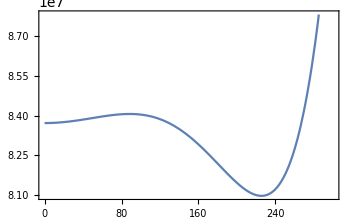

```mathematica
Plot[V0T‵1d‵ALP,{h,0,300}]
```

```mathematica
VhighT‵ALP=(V0‵ALP‵series/.{A->Atree,λ->λtree,μHsq->μHsqtree,μSsq->μSsqtree,δ->2π/5,v->vnum/(√2),f->3*fc})+VFT‵highT//Simplify
```

0.0319617 h^4-0.00956371 h^3 T+h^2 (0.000161971 S^2-3.15859 S+0.16323 T^2-3875.3)+80.8432 S^2+191487. S+1.97114×10^8

```mathematica
VhighT‵ALP‵1d=VhighT‵ALP/.S->Spath1d/.{A->Atree,λ->λtree,μHsq->μHsqtree,μSsq->μSsqtree,δ->2π/5,v->vnum/(√2),f->3*fc}//Simplify
```

1/((1. h^2+499121.)^2)(0.0319617 h^8-0.00956371 h^7 T+h^6 (0.16323 T^2+12631.3)-9546.91 h^5 T+h^4 (162943. T^2-1.52785×10^9)-2.38253×10^9 h^3 T+h^2 (4.06642×10^10 T^2+1.06655×10^14)+2.08575×10^19)

```mathematica
V1d‵series=Series[VhighT‵ALP‵1d,{h,0,6}]//Normal//Simplify
```

h^6 (4.03897×10^-28 T^2+7.77404×10^-8)-0.0068402 h^4-0.00956371 h^3 T+h^2 (0.16323 T^2+92.6371)+8.37241×10^7

```mathematica
Coefficient[V1d‵series,h^2]
Coefficient[V1d‵series,h^3]//Simplify
Coefficient[V1d‵series,h^4]//Simplify
Coefficient[V1d‵series,h^6]//Simplify
```

0.16323 T^2+92.6371

-0.00956371 T

-0.0068402

4.03897×10^-28 T^2+7.77404×10^-8

So the quartic term is actually negative here! The stability of the potential is now protected by the h^6 term.

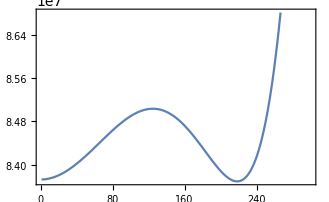

```mathematica
Ttest=26;
Plot[V1d‵series/.{T->Ttest},{h,1,300}]
```

```mathematica
Vsim‵highT=V‵Sim‵0+VFT‵highT/.{A->Atree,λ->λtree,μHsq->μHsqtree,μSsq->μSsqtree,δ->π/2,v->vnum/(√2)}
```

0.0319617 h^4-0.00956371 h^3 T-3.32114 (h^2-60624.1) S+0.16323 h^2 T^2-3875.3 h^2+90.6626 S^2

```mathematica
Spath‵sim=S/.Solve[D[Vsim‵highT,S]==0,S][[1]]//Normal
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

5.88572×10^-22 (3.11193×10^19 h^2-1.88658×10^24)

```mathematica
Vsim‵1d=Vsim‵highT/.{S->Spath‵sim}//Simplify
```

0.00154675 h^4-0.00956371 h^3 T+h^2 (0.16323 T^2-187.541)-1.11783×10^8

```mathematica
Ttest=35.6;
Plot[Vsim‵1d/.{T->Ttest},{h,1,200}]
```

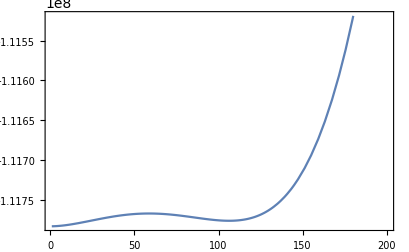
## 